# Calculating Vectorial Capacity

## Introductory discussion

Vectorial Capacity is defined as “the number of infectious bites that arise from all the mosquitoes that are infected by a single infectious person on a single day.”  That is to say, we pick a single infectious person and look at all of the mosquitoes who bite that person on one day.  We then follow each of those mosquitoes and count the number of infectious bites that occur between the time when the mosquito becomes infectious (after the incubation period) and the time when the mosquito dies.

When it comes to our simplified model of mosquito movement, we will consider all of the infectious biting events to result in the transmission of a parasite from the host to the vector and from the vector to the host.  
	• We have no hosts in our model so we can’t say how likely each host is to be infected.  
	• We could of course add some assumptions about the efficiency of transfer from hosts to vectors, but those would only add some multiplicative constants to each infection event

We will also consider every single infection to be independent, such that every vector may be infected by an unbounded number of independent parasite strains.  This allows us to simply count the number of infectious bites that arise from *each* biting event

We will assume that each mosquito’s biological needs require it to fly between egg laying/resting sites and blood feeding sites.  (There are of course other types of sites where the mosquito might visit, but for now we will ignore these)

We will assume that every visit to a blood feeding site results in 1 bite of a host, and will treat each bite as transferring parasite from the host to the vector.  (Whether or not the bite results in transferring parasite from the infectious vector to the host is not relevant to how vectorial capacity is defined - only biting conditioning on being infectious, no biting conditioning on successful transmission.)

## Creating a landscape, defining transition matrix

The landscape will allow us to define a transition matrix which we can use as a Markov transitions matrix.

All of this is borrowed from Hector’s Walking Dead Malaria scripts

### Functions

```mathematica
SetDirectory[NotebookDirectory[]]
(*Movement Kernels*)
CalculateEuclideanDistances[coordinatesSet_]:=Table[N[EuclideanDistance[coordinatesSet[[i]],#]]&/@coordinatesSet,{i,1,coordinatesSet//Length }]
(* This one is out of date; use the exponential one instead:
CalculateInverseLinearKernelMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce] *)
ExponentialKernel[λ_,distance_]:=λ*ⅇ^(-λ*distance)
(*Markov - Calculates fraction of time mosquitoes spend at each network node, given a Markov process
migrationProbabilities = transitions probability matrix, calculated using Euclidean distances and a Kernel *)
CalculateMarkovSteadyState[migrationProbabilities_]:=Module[{initialState,markov,markovPDF},
initialState=ConstantArray[0,migrationProbabilities//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,migrationProbabilities];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
markovPDF
]
(*Networks Plot*)
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[EdgesStyleList]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.025],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
VertexNumberToVertexSyllable[syllables_,fixedEdgesList_]:=Table[DirectedEdge[syllables[[fixedEdgesList[[index]][[1]][[1]]]],syllables[[fixedEdgesList[[index]][[1]][[2]]]]->fixedEdgesList[[index]][[2]]]//N,{index,1,Length[fixedEdgesList]}]
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,PlotTheme->"LakeNetwork",EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
(*Plots Styles*)
Themes`AddThemeRules["LakeMatrixPlot"
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,ColorFunction->ColorData[{"LakeColors","Reverse"}]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,ImageSize->250
,PlotRangePadding->0
]
Themes`AddThemeRules["LakeNetwork",
,EdgeShapeFunction->edgeshape2
,Epilog->Riffle[ConstantArray[Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]],sampledCoordinates//Length],(Disk[#,.25]&/@sampledCoordinates)]
,ImageSize -> 500
,ImagePadding->25
,LineThickness -> .0075
,VariableStyle->"Both"
,VertexCoordinates ->sampledCoordinates
,VertexSize ->.01
,VertexLabelStyle->.001
]
(*USES GLOBALS!*)
GraphPlotWrapper[migrationMatrix_,max_,vertexSize_,vertexStyle_]:= GraphTransitionsFrequenciesWithMax[
  {
migrationMatrix,
ToString /@ Range[Length[migrationMatrix]]
   }, max
,EdgeShapeFunction->edgeshape2
,ImagePadding->0
,ImageSize->imageSize
,LineThickness->lineThickness
,VariableStyle->"Both"
,VertexCoordinates->sampledCoordinates
,VertexSize -> vertexSize
,VertexStyle->vertexStyle
,VertexLabelStyle->.0001
  ]
```

/Users/dtcitron/Documents/MosPopDyn/MoNeT/MoNeT/Dev/DanielCitron

LakeMatrixPlot

LakeNetwork

### Inputs

#### Style

```mathematica
edgeChopThreshold=10^-1.5;
edgeshape2[e_,___]:={Arrowheads[{{.000000001,1}}],Arrow[e]}
lineThickness=.0005;
imageSize=250;
```

#### Parameters for generating landscape

```mathematica
(* Define:
nodesNumber - {size of grid, distance between nodes}, used as a way of generating all the different nodes on a grid;
 networkDimension - number of node types;
 distance - distance between cities;
*)
{nodesNumber,networkDimension,distance}={{100,50},2,50};
(**)
movementProbabilitiesVector=If[networkDimension>1,ConstantArray[0,networkDimension]//ReplacePart[#,{2->1,3->0}]&,ConstantArray[0,networkDimension]//ReplacePart[#,{1->1}]&];
(**)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,networkDimension}];
MatrixForm[penalizationsMatrix]
```

(0 | 1
1 | 0)

#### Random Walks

```mathematica
{chainsSteps,chainsNumber}={20,30};
```

### Generate Landscape

```mathematica
citiesSqrt=Range[0,nodesNumber[[1]],nodesNumber[[2]]];
sampledCoordinates=Tuples[citiesSqrt,2];
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
euclideanDistances=CalculateEuclideanDistances[sampledCoordinates];
```

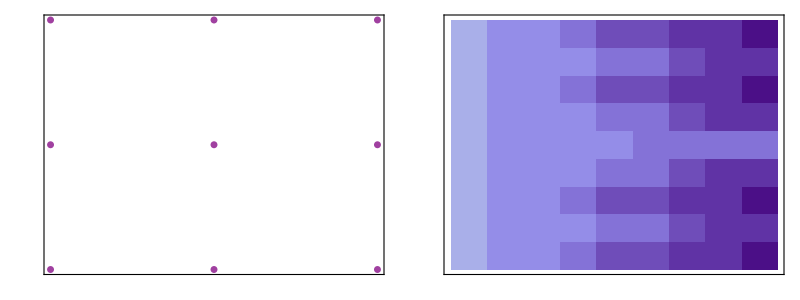

```mathematica
(*Visualize*)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clusteredCoordinates])]]//Flatten//RandomSample;
gridCoordinatesPlot=ListPlot[clusteredCoordinates//Flatten[#,1]&
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,GridLines->None
,GridLinesStyle->Directive[Gray,Opacity[.5],Dashed]
,ImageSize->250
,PlotRangePadding->.5
,PlotStyle->Directive[Purple,EdgeStyle[Black],Opacity[.75],PointSize[.02]]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,FrameTicksStyle->15
];
matrixDistancesPlot=MatrixPlot[Sort/@euclideanDistances,PlotTheme->"LakeMatrixPlot"];
Grid[{{gridCoordinatesPlot,matrixDistancesPlot}}]
```

### Movement Kernel

Use an exponential Kernel

```mathematica
migrationProbabilities=(#/Total[#])&/@ReplacePart[ExponentialKernel[0.01848777,#]&/@euclideanDistances,{i_,i_}->0];
```

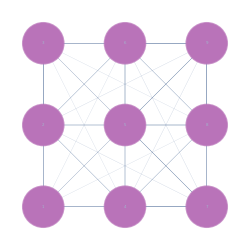

```mathematica
(*Visualize*)
matrixMigrationPlot=MatrixPlot[Sort/@migrationProbabilities,PlotTheme->"LakeMatrixPlot"];
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
originalMap=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,.05*edgeChopThreshold],.1,
(#->.5)&/@(ToString/@Range[migrationProbabilities//Length]),
stylesListType
]
```

### Markov Baseline

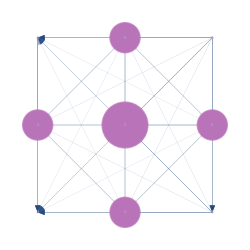

```mathematica
baselineMarkovSS=CalculateMarkovSteadyState[migrationProbabilities];
(*Visualize*)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
markovBaseline=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,.05*edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[.5+7.5*Rescale[baselineMarkovSS]]],
stylesListType
]
```

### Network Dimensionality (aka n-partite-ness)

{2,1,1,1,1,2,2,1,1}

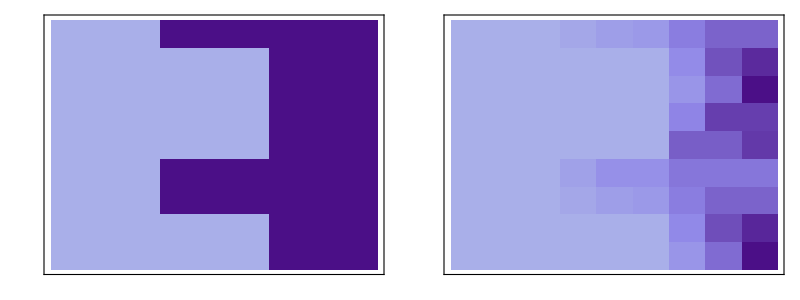

```mathematica
(* Vector of node types*)
nodeType=RandomChoice[Range[networkDimension],sampledCoordinates//Length]
dimensionalPenalizationsMask=Table[penalizationsMatrix[[i,#]]&/@nodeType,{i,nodeType}]; (* Very elegant way of generating full matrix of how we're re-weighting all edges according to the movement Kernel.  This includes both the multitype transition Penalization Mask and the baseline Markov connectivity *)
migrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*migrationProbabilities);
(**)
matrixPenalizationsPlot=MatrixPlot[Sort/@dimensionalPenalizationsMask,PlotTheme->"LakeMatrixPlot"];
matrixDimensionalPlot=MatrixPlot[Sort/@migrationDimensionalMatrix,PlotTheme->"LakeMatrixPlot"];
Grid[{{matrixPenalizationsPlot,matrixDimensionalPlot}}]
```

## Synthesizing : Markov Dimensional Network

(0. | 0.279163 | 0.110765 | 0.279163 | 0.190357 | 0. | 0. | 0.0890493 | 0.051502
0.499782 | 0. | 0. | 0. | 0. | 0.340794 | 0.159424 | 0. | 0.
0.250923 | 0. | 0. | 0. | 0. | 0.632407 | 0.116671 | 0. | 0.
0.417227 | 0. | 0. | 0. | 0. | 0.165545 | 0.417227 | 0. | 0.
0.288473 | 0. | 0. | 0. | 0. | 0.423053 | 0.288473 | 0. | 0.
0. | 0.143237 | 0.21006 | 0.0833464 | 0.21006 | 0. | 0. | 0.143237 | 0.21006
0. | 0.0890493 | 0.051502 | 0.279163 | 0.190357 | 0. | 0. | 0.279163 | 0.110765
0.159424 | 0. | 0. | 0. | 0. | 0.340794 | 0.499782 | 0. | 0.
0.116671 | 0. | 0. | 0. | 0. | 0.632407 | 0.250923 | 0. | 0.)

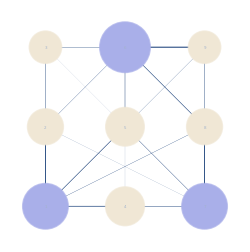

```mathematica
(* Calculate the steady state for our transitions matrix *)
markovPDF=CalculateMarkovSteadyState[migrationDimensionalMatrix];
(* Show the Markov transition matrix*)
MatrixForm[migrationDimensionalMatrix]
(*
Visualization:
  1. Node type is represented by color.
2. Frequency of visit in markov steady state represented by node diameter. 
3. Probability of transition represented by edge thickness
*)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[nodeType//Length],nodeType}];
markovDimensional=GraphPlotWrapper[
Chop[migrationDimensionalMatrix//LowerTriangularize,edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[5+7.5*Rescale[markovPDF]]],
stylesListType
]
```

## Ensembles of Trajectories

## Adding in Mosquito Death Transitions

```mathematica
MatrixForm[migrationDimensionalMatrix]
```

(0. | 0.279163 | 0.110765 | 0.279163 | 0.190357 | 0. | 0. | 0.0890493 | 0.051502
0.499782 | 0. | 0. | 0. | 0. | 0.340794 | 0.159424 | 0. | 0.
0.250923 | 0. | 0. | 0. | 0. | 0.632407 | 0.116671 | 0. | 0.
0.417227 | 0. | 0. | 0. | 0. | 0.165545 | 0.417227 | 0. | 0.
0.288473 | 0. | 0. | 0. | 0. | 0.423053 | 0.288473 | 0. | 0.
0. | 0.143237 | 0.21006 | 0.0833464 | 0.21006 | 0. | 0. | 0.143237 | 0.21006
0. | 0.0890493 | 0.051502 | 0.279163 | 0.190357 | 0. | 0. | 0.279163 | 0.110765
0.159424 | 0. | 0. | 0. | 0. | 0.340794 | 0.499782 | 0. | 0.
0.116671 | 0. | 0. | 0. | 0. | 0.632407 | 0.250923 | 0. | 0.)

```mathematica
mosHazardRates = Table[.1,{i,1,Length[sampledCoordinates]}];
```

```mathematica
mosMatrix = Join[Table[Join[migrationDimensionalMatrix[[i]]*(1-mosHazardRates[[i]]),{mosHazardRates[[i]]},1],{i,1,Length[migrationDimensionalMatrix]}],{Join[Table[0,{i,1,Length[migrationDimensionalMatrix]}],{1.}]},1];
```

```mathematica
MatrixForm[mosMatrix]
```

(0. | 0.251247 | 0.0996883 | 0.251247 | 0.171322 | 0. | 0. | 0.0801444 | 0.0463518 | 0.1
0.449804 | 0. | 0. | 0. | 0. | 0.306715 | 0.143481 | 0. | 0. | 0.1
0.22583 | 0. | 0. | 0. | 0. | 0.569166 | 0.105004 | 0. | 0. | 0.1
0.375505 | 0. | 0. | 0. | 0. | 0.148991 | 0.375505 | 0. | 0. | 0.1
0.259626 | 0. | 0. | 0. | 0. | 0.380748 | 0.259626 | 0. | 0. | 0.1
0. | 0.128913 | 0.189054 | 0.0750117 | 0.189054 | 0. | 0. | 0.128913 | 0.189054 | 0.1
0. | 0.0801444 | 0.0463518 | 0.251247 | 0.171322 | 0. | 0. | 0.251247 | 0.0996883 | 0.1
0.143481 | 0. | 0. | 0. | 0. | 0.306715 | 0.449804 | 0. | 0. | 0.1
0.105004 | 0. | 0. | 0. | 0. | 0.569166 | 0.22583 | 0. | 0. | 0.1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

## Examining a Single Trajectory

```mathematica
(* Start by generating an ensemble *)
init = Table[0,{i,1,Length[mosMatrix]}];
init[[1]]=1;  (* {2,1,1,1,1,2,2,1,1}*)
P = DiscreteMarkovProcess[init,mosMatrix];
RandomSeed[0];
mosEnsemble = RandomFunction[P, {0,100},10];
```

```mathematica
(* Define the Entomological Incubation Period *)
EIP = 10;
```

```mathematica
(* Select a chain *)
chainIndex = 4;
mosChain = mosEnsemble["Paths"][[chainIndex]];
(* Restrict to only time steps where the mosquitoes are not dead *)
mosChain = Cases[mosChain,{_,a_}/;a<10]
(* Time of death *)
tDeath = Length[mosChain]
```

{{0,1},{1,3},{2,6},{3,4},{4,7},{5,4},{6,1},{7,4},{8,7},{9,4},{10,7},{11,2},{12,1},{13,2}}

14

```mathematica
(* Look at the node type at each place visited, just to verify we're alternating *)
pathNodeTypes = (nodeType[[#]]&/@nodeType[[#]])&/@mosChain[[;;,2]];
(* Add the type visited to each row of the mosChain matrix *)
mosChain = Transpose[Join[Transpose[mosChain],{pathNodeTypes}]];
```

```mathematica
(* These are all of the indexes of the relevant starting positions
"Relevant" here means that they occur early enough that the mosquitoes do not die before the end of the EIP *)
tIndexes =  Position[mosChain[[;;Max[tDeath-EIP,1]]], {_,_,1}]//Flatten
```

{2,4}

```mathematica
(* Count visits to blood feeding sites following an initial infection at each blood feeding site *)
i = tIndexes[[1]]
(* And the initial position *)
j = mosChain[[i,2]]
```

2

3

```mathematica
(* The time steps that occur between end of EIP and mosquito death *)
subMosChain = mosChain[[i+EIP;;tDeath]]
(* Find where the secondary infectious occur:
Find the Location of all rows in the subChain where we visit a feeding site *)
bitesMosChain = Cases[subMosChain,{_,_,1}][[;;, 2]]
```

{{11,2,1},{12,1,2},{13,2,1}}

{2,2}

For the example above, we would say that a mosquito who was initially infected at site 3 then lived long enough to bite 2 more people at site 2

```mathematica
(* Repeating, but for the 2nd index *)
(* Count visits to blood feeding sites following an initial infection at each blood feeding site *)
i = tIndexes[[2]]
(* And the initial position *)
j = mosChain[[i,2]]
(* The time steps that occur between end of EIP and mosquito death *)
subMosChain = mosChain[[i+EIP;;tDeath]]
(* Find where the secondary infectious occur:
Find the Location of all rows in the subChain where we visit a feeding site *)
bitesMosChain = Cases[subMosChain,{_,_,1}][[;;, 2]]
```

4

4

{{13,2,1}}

{2}

So in addition this same mosquito who bit someone at site 4 lived long enough to also bite someone at site 2.

## Calculate VC-influence matrix

What I call the VC-influence matrix is the number of secondary bites that occur at site j given that the initial bite occurred at site i.  If we sum over all target sites j we obtain the Vectorial Capacity for each site i.

```mathematica
(* Start by generating an ensemble *)
init = Table[0,{i,1,Length[mosMatrix]}];
init[[1]]=1;  (* {2,1,1,1,1,2,2,1,1}*)
P = DiscreteMarkovProcess[init,mosMatrix];
mosEnsemble = RandomFunction[P, {0,100},1000];
```

```mathematica
(* Define the Entomological Incubation Period *)
EIP = 10;
(* Define VCI, where VCI[[i,j]] = Number of bites at j following an infectious bite at i *)
VCI = Table[0,{i,1,Length[migrationDimensionalMatrix]},{j,1,Length[migrationDimensionalMatrix]}];


Do[
(* Select a chain *)
mosChain = mosEnsemble["Paths"][[chainIndex]];
mosChain = Cases[mosChain,{_,a_}/;a<10];
tDeath = Length[mosChain];
(* Look at the node type at each place visited, just to verify we're alternating *)
pathNodeTypes = (nodeType[[#]]&/@nodeType[[#]])&/@mosChain[[;;,2]];
(* Add the type visited to each *)
mosChain = Transpose[Join[Transpose[mosChain],{pathNodeTypes}]];

(* These are all of the indexes of the relevant starting positions *)
tIndexes =  Position[mosChain[[;;Max[tDeath-EIP,1]]], {_,_,1}]//Flatten;
(* Count visits to blood feeding sites following initial infection at each blood feeding site *)
Do[ (* Loop over all starting indices *)
(* Subset our chain according to the times when secondary infections could occur
Between t = i + EIP and tDeath *)
subMosChain = mosChain[[i+EIP;;tDeath]];
(* Find where the secondary infectious occur:
Find the Location of all rows in the subChain where we visit a feeding site *)
bitesMosChain = Cases[subMosChain,{_,_,1}][[;;, 2]]; 
Do[ (* Add biting event counts *)
VCI[[mosChain[[i,2]],bitesMosChain[[j]]]]+=1,
{j,1,Length[bitesMosChain]}]
(* End *)
,{i,tIndexes}],
(* End loop over chain *)
{chainIndex,1,mosEnsemble["PathCount"]}]
```

```mathematica
(* Visualize the VC-influence matrix*)
MatrixForm[1.*VCI/mosEnsemble["PathCount"]]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.269 | 0.213 | 0.352 | 0.307 | 0. | 0. | 0.285 | 0.187
0. | 0.168 | 0.108 | 0.198 | 0.201 | 0. | 0. | 0.159 | 0.116
0. | 0.326 | 0.201 | 0.34 | 0.303 | 0. | 0. | 0.301 | 0.19
0. | 0.286 | 0.236 | 0.367 | 0.314 | 0. | 0. | 0.302 | 0.226
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.198 | 0.156 | 0.263 | 0.255 | 0. | 0. | 0.229 | 0.145
0. | 0.136 | 0.105 | 0.193 | 0.196 | 0. | 0. | 0.173 | 0.097)

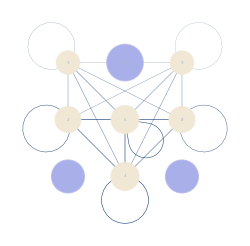

```mathematica
(* Network Visualization of the VC-influence matrix *)
markovPDF=CalculateMarkovSteadyState[migrationDimensionalMatrix];
(**)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[nodeType//Length],nodeType}];
markovDimensional=GraphPlotWrapper[
Chop[(1.*VCI/mosEnsemble["PathCount"])//LowerTriangularize,edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[5+7.5*Rescale[markovPDF]]],
stylesListType
]
```